# A fast marching solver with adaptive stencils

This Mathematica notebook is intended as a companion notebook for the manuscript : Jean - Marie Mirebeau, Jorg Portegies, "Hamiltonian Fast Marching: A numerical solver for anisotropic and non-holonomic eikonal PDEs", 2018 (submitted) and as documentation for the HamiltonFastMarching (HFM) library, which also has interfaces to the Matlab® and Python languages. For a more extended version of this notebook in Python, see here, and for an overview of other Python notebooks demonstrating the HFM library functionality, see this summary.

 The present notebook, shows how the HFM software can solve isotropic eikonal equations and extract the related minimal paths. The assumption of isotropy makes this task rather simple and classical, and more complex models are addressed in the subsequent notebooks. We present some two and three dimensional test cases, featuring obstacles, position and eventually time - dependent velocities, various stopping criteria, ...
 
The functionality presented in this notebook, in the context of isotropic fast marching, is also applicable to the more complex anisotropic models implemented in the HFM software.

## A. Showcase of the HFM library functionality

I - Classical isotropic fast marching

## Directory settings

In this series of notebooks, input and output to the HamiltonFastMarching library is based on files written on the disk. Change the following directory settings to work on your own machine.

```mathematica
(*directory with fast marching executable*)
(*hfmexeDirectory = "C:\\Users\\jportegi\\stack\\PostDoc\\Fast-Marching\\HamiltonFastMarching-master\\binminsizerel\\"; (*Windows format*)*)
hfmexeDirectory = "/Users/mirebeau/bin/2018/FileHFM/Release"; (*Linux/MacOs format*)

(*directory where experiments should be placed*)
hfmoutputDirectory=FileNameJoin[{NotebookDirectory[],"experiments"}];

(*In case hfmoutputDirectory does not exist, it needs to be created*)
If[!DirectoryQ[hfmoutputDirectory],CreateDirectory[hfmoutputDirectory]]
```

## Functions to call external Fast Marching solver

```mathematica
(*Function to call the HFM executable with the desired parameters, and import the result to Mathematica*)
runHFM[experimentName_,params_]:=Module[{model,execPrefix,output},

execPrefix=If[$OperatingSystem=="Windows","","./"];

model="model"/.params;

If[RulesToRaw[params,FileNameJoin[{hfmoutputDirectory,experimentName<>"_input"}]],Print["Failed to export params"];Return[];];

Run[FileNameJoin[{hfmexeDirectory,execPrefix<>"FileHFM_"<>model}]<>" "
<>FileNameJoin[{hfmoutputDirectory,experimentName<>"_input"}]<>" "
<>FileNameJoin[{hfmoutputDirectory,experimentName<>"_output"}] <>" > "
<>FileNameJoin[{hfmoutputDirectory,"log.txt"}]];

output=RawToRules[FileNameJoin[{hfmoutputDirectory,experimentName<>"_output"}]];
AppendTo[output,"log"->Import[FileNameJoin[{hfmoutputDirectory,"log.txt"}]]];

Map[If[StringContainsQ[#,"geodesicPoints"],suffix=StringSplit[#,"geodesicPoints"];AppendTo[output,"geodesics"<>suffix->dynP["geodesicPoints"<>suffix/.output,Round["geodesicLengths"<>suffix/.output]]]];&,First/@output];

Return[output]]
```

```mathematica
(*dynP is Dynamic partition, from http://mathematica.stackexchange.com/a/7512.*)
dynP[l_,p_]:=MapThread[l[[#;;#2]]&,{{0}~Join~Most@#+1,#}&@Accumulate@p];
MergeRules[provided_,default_]:=With[{l=First/@provided},Join[provided,Select[default,Not@MemberQ[l,First@#]&]]];
TablePlot[t_,opts_:{}]:=ArrayPlot@@Prepend[opts,Reverse@Transpose@t];
```

```mathematica
(* -------- Copied from FileIO.nb, in JMMCPPLibs/Output --------*)
(*Auxilary functions for writing and reading input and output files*)
RulesToRaw[l_List,fileName_String]:=Module[{
lStr , lNum, lArr,
str="",data={}
},
With[{bad=Select[l,Length@#!=2&]},
If[bad≠{},Print["SaveToFile Error : Elements of l are not pairs\n",Short[bad,2]];
 Return[True];]];

With[{bad=Select[l,!StringQ@First@#&]},
If[bad≠{},Print["SaveToFile Error : Keys are not strings\n",Short[bad,2]];
 Return[True];]];

With[{bad=Select[l,!(StringQ@#||NumericQ@#||ArrayQ[#,_,NumericQ]||#===Null)&@Last[#]&]},
If[bad≠{},Print["SaveToFile Error : data format should be string|Numeric|Array\n",Short[bad,2]];
 Return[True];]];

lStr=Select[l,StringQ@Last@#&];
lNum=Select[l,NumericQ@Last@#&];
lArr=Select[l,ArrayQ@Last@#&];

Do[
str=str<>(First@eStr)<>"\n-1\n"<>(Last@eStr)<>"\n\n";
,{eStr,lStr}];

Do[
str=str<>(First@eNum)<>"\n0\n\n";
AppendTo[data,N@Last@eNum];
,{eNum,lNum}];

Do[
With[{dims=Dimensions@Last@eArr}, (*Row major*)
str=str<>(First@eArr)<>"\n"
<>ToString[Length@dims]<>"\n";
Do[str=str<>ToString[d]<>"\n",{d,dims}];
str=str<>"\n";
];
data=Join[data,N@Flatten@Last@eArr];
,{eArr,lArr}];

If[StringLength[fileName]>0,
With[{formatFile=fileName<>"_Format.txt",dataFile=fileName<>"_Data.dat"},
Export[formatFile,str]; (*Mathematica adds one \n, so we must remove one...*)
If[Length@data>0,BinaryWrite[dataFile,data,"Real64"]; Close[dataFile];];
Return[False];
],
Return[{str,data}];
];
];

RawToRules[fileName_String]:=Module[{formatFile=fileName<>"_Format.txt",dataFile=fileName<>"_Data.dat",data},
RawToRules[Import[formatFile,"String"],BinaryReadList[dataFile,"Real64"]]
]

RawToRules[str_String,data_List]:=Module[{l={},pos=0,newlineCharacter=If[$OperatingSystem=="Windows","\r\n","\n"]},
Do[
Module[{format = StringSplit[s,newlineCharacter],dim,dims,oldPos=pos,oldLen=Length@l},
If[Length@format≥2,
dim=ToExpression[format[[2]]];
If[IntegerQ[dim] && dim≥-1,
If[dim==-1,
If[Length@format==3,AppendTo[l,format[[1]]->format[[3]] ] ],
If[Length@format==dim+2,
dims=Table[ToExpression@format[[i+2]],{i,dim}]; (*row major*)
pos=pos+Times@@dims;
If[Length@data≥pos,AppendTo[l,format[[1]]-> ArrayReshape[data[[oldPos+1;;pos]],dims] ]]
] ] ] ];
(*Allow for a final blank line*)
If[Length@l==oldLen && s≠newlineCharacter,Print["RawToRules error : could not import "<>s]];
]
,{s,StringSplit[str,newlineCharacter<>newlineCharacter]}];
l
]
```

## Description of the problem

In this document, we solve the standard isotropic eikonal equation, on domain denoted Ω. A cost function c : Ω → (0,∞) and some boundary data σ : ∂Ω → (-∞,∞] are given. This partial differential equation (PDE) reads:

∀x∈Ω,‖∇u[x]‖=c[x],∀x∈∂Ω,u[x]=σ[x].

This PDE admits a unique viscosity solution to this PDE, defined as follows. The solution value u[x] is the minimal length (plus initial value penalization) of a path γ:[0,1]→ Ω̄ from the domain boundary ∂Ω to x:

u[x]=inf_(γ[1]=x) σ[γ[0]]+(∫_0)^1 c[γ[t]]‖γ'[t]‖ dt.

Equivalently, the solution u can be regarded as the arrival time at x∈Ω of a front originating from  ∂Ω at time σ: ∂Ω→(-∞,∞], and propagating at speed s=1/c, where c:Ω→ (0,∞).

```mathematica
model="Isotropic2"; (*to model isotropic 2D eikonal equation*)
sndOrder=1.; (*use a second order scheme, to increase accuracy *)
cost=1. ; (*position-independent cost for now*)
(*speed=1.; one may provide a speed function instead of a cost function, in which case cost = 1/speed; *)
```

Our domain will be the rectangle [-1,1]×[0,1], discretized on a 2n × n grid, where n = 100.

```mathematica
n=100;
dims={2n,n};
gridscale=1./n;
origin={-1.,0.};
```

The discretized grid consists of the following points:

```mathematica
grid=Table[({i,j}-0.5)*gridscale+origin,{i,dims[[1]]},{j,dims[[2]]}];
```

We use the seed points ‘seeds’, and we initialize their values with ‘seedValues’.

```mathematica
seeds={{-0.5,0.3},{0.5,0.8}};
seedValues={0.,0.5};
```

We specify the kind of output that we want from the solver:

```mathematica
exportValues=1; (*ask for the solution of the PDE*)
exportGeodesicFlow=1; (*ask for the geodesic flow direction, computed from the numerical scheme's upwind gradients*)
```

We ask for geodesics from the following endpoints ‘tips’:

```mathematica
tips={{0.,0.6},{-0.9,0.5},{0.8,0.8}};
(*geodesicSolver = "ODE"; choose the backtracking method. Defaults to 'Discrete' if unspecified*)
```

The ordering the first two entries can be transposed, if desired:

```mathematica
arrayOrdering = "YXZ_RowMajor";
```

#### Isotropic2 example

We store all fast marching parameters in a list of rules in the variable ‘params’:

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->1.,
"sndOrder"->sndOrder
};
```

Using the function runHFM (defined earlier in this notebook), we call the fast marching solver with the desired parameters, and we name the experiment “test”. The result is stored in the variable ‘output’.

```mathematica
output=runHFM["test",params];
"log"/.output (*by displaying the log, we see how the computation went*)
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.006854 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

We can import geodesics as well as the value function, the solution to the eikonal PDE:

```mathematica
geodesics="geodesics"/.output;
values="values"/.output;
```

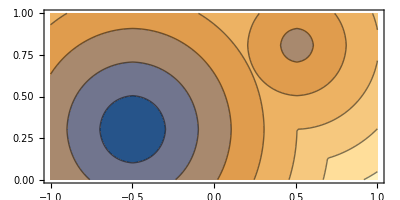

```mathematica
contourplot=ListContourPlot[values,DataRange->{{-1,1},{0,1}},AspectRatio->1/2]
```

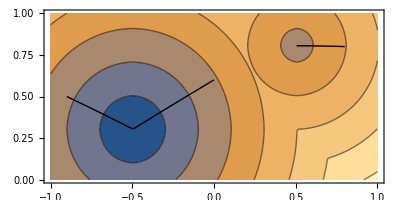

```mathematica
Show[{contourplot,Graphics[Line[geodesics]]}]
```

The minimal geodesics associated with our path planning problem obey an Ordinary Differential Equation (ODE), defined in terms of the solution u of the eikonal PDE. More precisely, the minimal geodesic reaching the point x∈Ω at the time T=u(x) obeys

∀t≤T, γ'[t]=V[γ[t]], γ[T]=x.

In practice, this ODE is solved backwards in time, as evidenced by the terminal boundary condition γ[T]=x.

The vector field V : Ω → ℝ^2, displayed in the next cell, is referred to as the geodesic flow direction, and is expressed in terms of the gradient of the arrival times function u:Ω→ ℝ. In the case of an isotropic metric, defined by a cost function c:Ω → (0,∞):

V[x]=c[x]^-2∇u[x]

We can import and display the vector field:

```mathematica
geodesicflow="geodesicFlow"/.output;
```

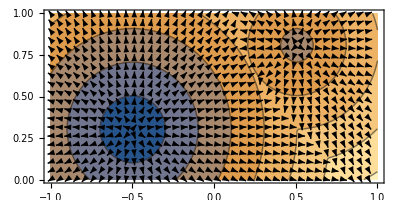

```mathematica
Show[{contourplot,ListVectorPlot[Transpose[geodesicflow,{2,1}],VectorPoints->{40,20},DataRange->{{-1.,1.},{0.,1.}},VectorStyle->Black,VectorScale->0.02]}]
```

By construction, the geodesic flow has unit speed, as measured by the metric of the problem. In the present case of an isotropic metric, this is easily checked formally, since we get for each point x∈Ω

c[x]‖V[x]‖=c[x]^-1‖∇u[x]‖=1.

Note that this identity is not satisfied at the two seed points, which strictly speaking are part of ∂Ω. We check this identity numerically:

```mathematica
norms=Map[("cost"/.params)Norm[#]&,geodesicflow,{2}];
```

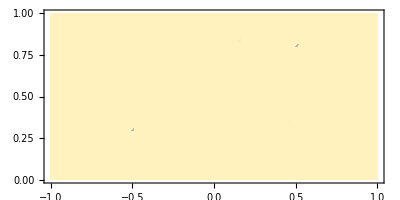

```mathematica
ListDensityPlot[norms,DataRange->{{-1.,1.},{0.,1.}},PlotRange->{0,1.1},AspectRatio->1/2,PlotLegends->Automatic]
```

## Introducing obstacles and a position-dependent speed

An obstacle is described as an array of 0 (obstacle absent) or 1 (obstacle present). One-pixel-thin structures can be used to represent walls. In the case, considered in the following notebooks, where adaptive wide stencil discretization schemes are used, a test is done to ensure that the scheme offsets do not jump over the walls.

```mathematica
(*auxiliary function to define circular obstacle*)
diskfunction[x_,y_]:=If[(x-0.3)^2+(y-0.3)^2≤0.2^2,1,0];
```

```mathematica
obstacle=Map[diskfunction[Sequence@@#]&,Transpose@grid,{2}];
```

```mathematica
obstacle[[40;;-1,70]]=1;
```

Obstacles introduced in the domain:

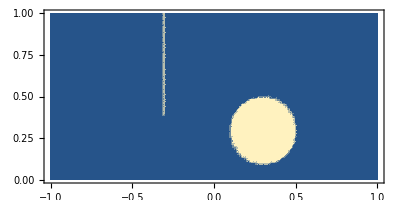

```mathematica
ListDensityPlot[obstacle,DataRange->{{-1.,1.},{0.,1.}},AspectRatio->1/2]
```

We also introduce a position-dependent cost function:

```mathematica
cost=Transpose@Map[Exp[-0.5(#⟦1⟧^2+#⟦2⟧^2)]&,grid,{2}];
```

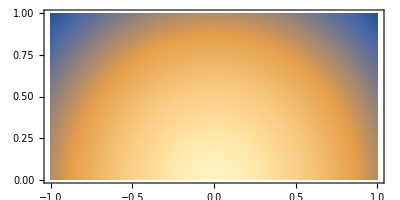

```mathematica
ListDensityPlot[cost,DataRange->{{-1.,1.},{0.,1.}},AspectRatio->1/2]
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"sndOrder"->sndOrder,
"walls"->obstacle
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.007342 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

```mathematica
geodesics="geodesics"/.output;
values="values"/.output;
```

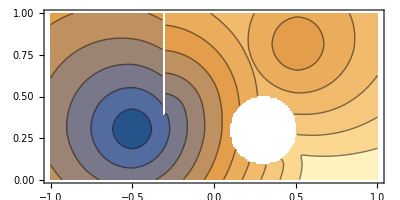

```mathematica
contourplot=ListContourPlot[values,DataRange->{{-1,1},{0,1}},AspectRatio->1/2,Contours->10]
```

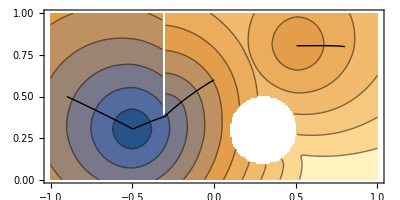

```mathematica
Show[{contourplot,Graphics[Line[geodesics]]}]
```

## Termination criteria

The HFM software by default terminates when eikonal PDE is solved on the entire domain Ω, by propagating a front in a single pass, in a Dijkstra - like manner.However it can be interesting to abort the computation early, in order for instance to save CPU time.Various stopping criteria are available for that purpose.

### Stop when all tips are reached by the wavefront

We provide an option for stopping the front propagation as soon as every member of a collection of points is reached.In many applications, the minimal geodesics are more valuable than the distance map itself.In that case, one may stop the front propagation as soon as all the geodesic tips are reached.Computation time is reduced, and geodesic backtracking is still feasible.

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"sndOrder"->sndOrder,
"walls"->obstacle, 
"stopWhenAllAccepted"->tips
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.005123 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

```mathematica
geodesics="geodesics"/.output;
values="values"/.output;
```

```mathematica
contourplot=ListContourPlot[values,DataRange->{{-1,1},{0,1}},AspectRatio->1/2,Contours->10]
```

-Graphics-

```mathematica
Show[{contourplot,Graphics[Line[geodesics]]}]
```

-Graphics-

### Stop when any of the tips is reached by the wavefront

A second option stops the front propagation as soon as any member of a collection of points is reached. For illustration, we stop as soon as the first geodesic tip is reached. The geodesic originating from this particular point can be backtraced, but obviously the others cannot anymore.

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"sndOrder"->sndOrder,
"walls"->obstacle, 
"stopWhenAnyAccepted"->tips
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.001651 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

```mathematica
geodesics="geodesics"/.output;
values="values"/.output;
```

```mathematica
contourplot=ListContourPlot[values,DataRange->{{-1,1},{0,1}},AspectRatio->Automatic,Contours->10]
```

-Graphics-

```mathematica
Show[{contourplot,Graphics[Line[geodesics]]}]
```

-Graphics-

### Stop at a fixed distance

We here decide to terminate the front propagation once the value function, i.e. the distance from the seeds (plus possibly the boundary condition), reaches a provided threshold.

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"sndOrder"->sndOrder,
"walls"->obstacle, 
"stopAtDistance"->0.7
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.006222 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

```mathematica
geodesics="geodesics"/.output;
values="values"/.output;
```

```mathematica
contourplot=ListContourPlot[values,DataRange->{{-1,1},{0,1}},AspectRatio->1/2,Contours->10]
```

-Graphics-

```mathematica
Show[{contourplot,Graphics[Line[geodesics]]}]
```

-Graphics-

## Side products of the fast marching algorithm

The HFM software can compute several side products in addition to the (approximate) distance map u:Ω→(−∞,∞]. In this section, we present two of them: the euclidean length of the minimal geodesics, and the Voronoi diagram associated with the seeds. Since these computations are performed simultaneously with the front propagation, they are also used within stopping criteria.

### Voronoi regions

The Voronoi cell of a seed consists of all the points which are closer to this seed than to the others.

```mathematica
seedflags={0,1};(*define voronoi region indices associated to the seed points*)
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"sndOrder"->sndOrder,
"walls"->obstacle, 
"seedFlags"->seedflags
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Field voronoiStoppingCriterion defaults to None
Fast marching solver completed in 0.006973 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0
Field exportVoronoiFlags defaults to 1

```mathematica
geodesics="geodesics"/.output;
values="values"/.output;
```

```mathematica
voronoiFlags="voronoiFlags"/.output;
```

```mathematica
contourplot=ListContourPlot[voronoiFlags,DataRange->{{-1,1},{0,1}},AspectRatio->1/2,Contours->10]
```

-Graphics-

```mathematica
Show[{contourplot,Graphics[Line[geodesics]]}]
```

-Graphics-

We can also stop the fast marching solver as soon as two voronoi regions meet:

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"sndOrder"->sndOrder,
"walls"->obstacle, 
"seedFlags"->seedflags,
"voronoiStoppingCriterion"->"RegionsMeeting"
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.005544 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0
Field exportVoronoiFlags defaults to 1
Field voronoiDiagram_exportGeodesicFromMeetingPoint defaults to 1

```mathematica
geodesics="geodesics"/.output;
values="values"/.output;
```

```mathematica
voronoiFlags="voronoiFlags"/.output;
```

```mathematica
voronoigeodesics="geodesics_voronoiDiagram"/.output;
```

```mathematica
contourplot=ListContourPlot[voronoiFlags,DataRange->{{-1,1},{0,1}},AspectRatio->1/2,Contours->10]
```

-Graphics-

```mathematica
Show[{contourplot,Graphics[Line[voronoigeodesics]]}]
```

-Graphics-

### Euclidean length of geodesics

A simple addition to the numerical scheme allows to compute the euclidean length of the minimal geodesics from the seeds towards the points of the fast marching front. Optionally, we may to interrupt the computations once these lengths reach a prescribed threshold. The scale of the grid must be specified in each direction.Optionally, this scale may vary over the domain.

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"euclideanScale"->{gridscale,gridscale},
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"sndOrder"->sndOrder,
"walls"->obstacle, 
"seedFlags"->{0,1},
"stopAtEuclideanLength"->.6
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Field voronoiStoppingCriterion defaults to None
Fast marching solver completed in 0.003024 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0
Field exportEuclideanLengths defaults to 1
Field euclideanLength_exportGeodesicFromStoppingPoint defaults to 1
Field exportVoronoiFlags defaults to 1

```mathematica
values="values"/.output;
```

```mathematica
geodesics="geodesics"/.output;
```

```mathematica
geodesicsEuclideanLength="geodesics_euclideanLength"/.output;
```

```mathematica
output[[All,1]]
```

{FMCPUTime,MaxStencilWidth,StencilCPUTime,defaulted,euclideanLength_stoppingPoint,euclideanLengths,geodesicFlow,geodesicLengths,geodesicLengths_euclideanLength,geodesicPoints,geodesicPoints_euclideanLength,nAccepted,unusedFromCompute,values,visitedUnset,voronoiFlags,log,geodesics,geodesics_euclideanLength}

```mathematica
contourplot=ListContourPlot[values,DataRange->{{-1,1},{0,1}},AspectRatio->Automatic,Contours->10]
```

-Graphics-

```mathematica
Show[{contourplot,Graphics[Line[geodesicsEuclideanLength]]}]
```

-Graphics-

As a consistency check, we compare the value function with the euclidean length of geodesics, the latter being computed with an adequately chosen point dependent scale. The two quantities are equal up to machine precision, as expected, on the voronoi region of the left seed. On the voronoi region of the right seed, they differ by the seed boundary value, namely 0.5.

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScale"->gridscale,
"euclideanScale"->Transpose[gridscale*{cost,cost},{3,1,2}],
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"walls"->obstacle, 
"seedFlags"->{0,1}
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field sndOrder defaults to 0
Field showProgress defaults to 0
Field voronoiStoppingCriterion defaults to None
Fast marching solver completed in 0.007171 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0
Field exportEuclideanLengths defaults to 1
Field exportVoronoiFlags defaults to 1

```mathematica
values="values"/.output;
euclideanLengths="euclideanLengths"/.output;
```

```mathematica
geodesics="geodesicPoints"/.output;
```

```mathematica
contourplot=ListContourPlot[Abs[values-euclideanLengths],DataRange->{{-1,1},{0,1}},AspectRatio->1/2,Contours->10]
```

-Graphics-

## Using a time dependent speed function

We can also define a speed function that depends on time, with a finite number of time intervals. In the next example, we have three times ‘speedTimes’ for which the speeds ‘speed0’, ‘speed1’ and ‘speed2’ are defined. The code linearly interpolates the speed functions in between those times. Before the smallest and after the largest time, the speed functions are constant (w.r.t. time).

```mathematica
exportGeodesicFlow=0.;
```

```mathematica
speedTimes={0.2,0.6,1.4};
speed0=Transpose@Map[Exp[0.5(#⟦1⟧^2+#⟦2⟧^2)]&,grid,{2}];
speed1=0.2 ;
speed2=speed0;
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seeds"->seeds,
"seedValues"->seedValues,
"gridScale"->gridscale,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"speed_times"->speedTimes,
"speed_0"->speed0,
"speed_1"->speed1,
"speed_2"->speed2,
"walls"->obstacle,
"sndOrder"->1.
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.00792 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

```mathematica
values="values"/.output;
geodesics="geodesics"/.output;
```

```mathematica
contourplot=ListContourPlot[values,DataRange->{{-1,1},{0,1}},AspectRatio->1/2,Contours->10]
```

-Graphics-

```mathematica
Show[{contourplot,Graphics[Line[geodesics]]}]
```

-Graphics-

## Three dimensional fast marching

We can apply the same theory in 3D (still with an isotropic metric). In this case, the code is called as follows:

```mathematica
model="Isotropic3";
arrayOrdering="RowMajor"; (*ListContourPlot3D works with XYZ ordering*)
n3D=50;
dims={3n3D,2n3D,n3D};
gridscale=1./n3D;
seeds={{0.3,0.5,0.7}};
```

```mathematica
grid3D=Table[({i,j,k}-0.5)*gridscale,{i,3n3D},{j,2n3D},{k,n3D}];
```

```mathematica
speed=Map[Exp[-(#[[1]]-1.5)^2-(#[[2]]-1)^2-(#[[3]]-0.5)^2]&,grid3D,{3}];
```

```mathematica
tips=Flatten[Table[({i,j,k}-0.5)*{1,2/3,1/3},{i,3},{j,3},{k,3}],2];
```

```mathematica
params = {"model"->model,
(*"seedValues"->seedValues,*)
"seeds"->seeds,
"gridScale"->gridscale,
(*"euclideanScale"->Transpose[gridscale*{cost,cost},{3,1,2}],*)
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->1/speed,
(*"speed"->speed,*)
(*"speed_2"->speed2,*)
(*"walls"->obstacle,*)
"sndOrder"->1.
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field origin defaults to {0,0,0}
Field showProgress defaults to 0
Fast marching solver completed in 0.568057 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 5.4925
Field exportActiveNeighs defaults to 0

```mathematica
values="values"/.output;
geodesics="geodesics"/.output;
```

```mathematica
ListContourPlot3D[Transpose[values,{3,2,1}],Contours->{1,3,5,10},DataRange->{{0,3},{0,2},{0,1}},BoxRatios->{3,2,1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[geodesics,PlotRange->{{0,3},{0,2},{0,1}}]
```

-Graphics3D-

## Diagonal metrics

With a minor adaptation to the isotropic case, we can consider diagonal metrics. The path cost takes the form

L_M[γ]:=(∫_0)^1(‖γ'[t]‖)_M[γ[t]]dt

where M[x] is a diagonal matrix, dependent on the current position x ∈Ω and the norm is defined as (‖v‖)_M=√⟨Mv,v⟩. The cost can be rewritten in the form

(‖ẋ[t]‖)_M[x]=√(∑_(1≤ i≤ d) c_i[x]^2)

The user inputs d cost functions, where d is the dimension, instead of a single cost function in the isotropic case. All the tools described in the isotropic case also apply to the diagonal models.

```mathematica
model="Diagonal2";
sndOrder=1.;
```

```mathematica
n=100;
dims={2n,n};
gridscale=1./n;
origin={-1.,0.};
```

```mathematica
grid=Table[({i,j}-0.5)*gridscale+origin,{i,dims[[1]]},{j,dims[[2]]}];
```

```mathematica
seeds={{-0.5,0.3},{0.5,0.8}};
seedValues={0.,0.5};
```

```mathematica
exportValues=1;
exportGeodesicFlow=1;
```

```mathematica
tips={{0.,0.6},{-0.9,0.5},{0.8,0.8}};
```

```mathematica
arrayOrdering = "YXZ_RowMajor";
```

```mathematica
cost=Map[Exp[-0.5(#⟦1⟧^2+#⟦2⟧^2)]&,grid,{2}];
cost=Transpose[{cost,1+0*cost},{3,2,1}];
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seedValues"->seedValues,
"seeds"->seeds,
"gridScales"->{gridscale,gridscale},
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"cost"->cost,
"walls"->obstacle,
"sndOrder"->sndOrder
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.008005 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

```mathematica
values="values"/.output;
geodesics="geodesics"/.output;
```

```mathematica
contourplot=ListContourPlot[values,DataRange->{{-1,1},{0,1}},AspectRatio->1/2,Contours->6]
```

-Graphics-

```mathematica
Show[{contourplot,Graphics[Line[geodesics]]}]
```

-Graphics-